```mathematica
SetDirectory[NotebookDirectory[]]；
xlist = Table[i,{i,-20,20,40/45359}];
xlist//Length
```

/Users/moe/comp_phys/neural_quantum_state/EXCITED NERONS/PRE/Data ； Null

45360

```mathematica
dataloader//Length
```

45360

```mathematica
"/Users/moe/comp_phys/neural_quantum_state/EXCITED NERONS/PRE/Data" ;
```

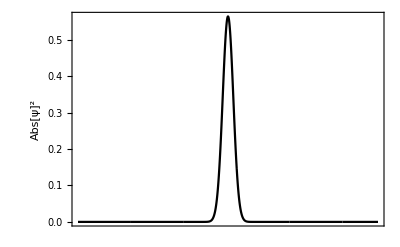

Ground_State.eps

```mathematica
(*dataloader = Import["Ground_State.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
ListLinePlot[dataloader^2,PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotStyle->{Black,Thick[0.01]}]
Export["Ground_State.eps",%]*)
```

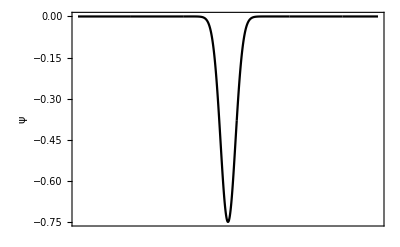

Ground_State.eps

```mathematica
dataloader = Import["Ground_State.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
ListLinePlot[dataloader,PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["\\psi",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotStyle->{Black,Thick[0.01]}]
Export["Ground_State.eps",%]
```

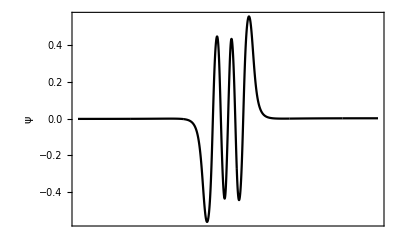

Excited_State_5.eps

```mathematica
dataloader = Import["Excited_State_5.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
ListLinePlot[dataloader,PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["\\psi",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotStyle->{Black,Thick[0.01]}]
Export["Excited_State_5.eps",%]
```

```mathematica
ψ[n_,x_]:=1/Sqrt[Sqrt[Pi] 2^n n!] Exp[-x^2/2] HermiteH[n,x];
```

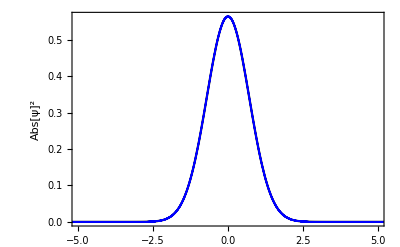

```mathematica
gs = Plot[Evaluate[ψ[0,x]^2],Evaluate@{x,-20,20},PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
dataloader = Import["Ground_State.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
dataloader = Thread[{xlist,dataloader^2}];
simgs=ListPlot[dataloader,PlotRange->All, Frame->True,PlotStyle->{Blue}, FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
Show[gs,simgs,PlotRange->{{-5,5},All}]
```

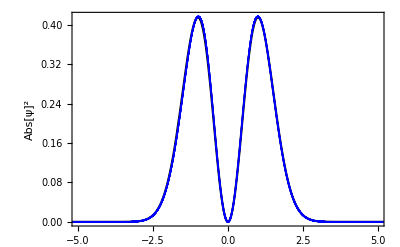

```mathematica
gs = Plot[Evaluate[ψ[1,x]^2],Evaluate@{x,-20,20},PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
dataloader = Import["Excited_State_1.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
dataloader = Thread[{xlist,dataloader^2}];
simgs=ListPlot[dataloader,PlotRange->All, Frame->True,PlotStyle->{Blue}, FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
Show[gs,simgs,PlotRange->{{-5,5},All}]
```

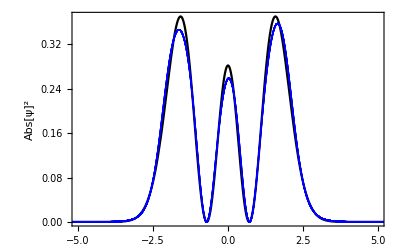

```mathematica
gs = Plot[Evaluate[ψ[2,x]^2],Evaluate@{x,-20,20},PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
dataloader = Import["Excited_State_2.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
dataloader = Thread[{xlist,dataloader^2}];
simgs=ListPlot[dataloader,PlotRange->All, Frame->True,PlotStyle->{Blue}, FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
Show[gs,simgs,PlotRange->{{-5,5},All}]
```

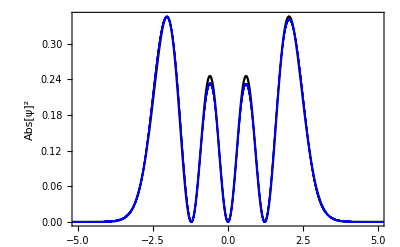

```mathematica
gs = Plot[Evaluate[ψ[3,x]^2],Evaluate@{x,-20,20},PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
dataloader = Import["Excited_State_3.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
dataloader = Thread[{xlist,dataloader^2}];
simgs=ListPlot[dataloader,PlotRange->All, Frame->True,PlotStyle->{Blue}, FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
Show[gs,simgs,PlotRange->{{-5,5},All}]
```

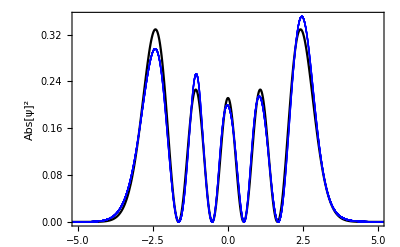

```mathematica
gs = Plot[Evaluate[ψ[4,x]^2],Evaluate@{x,-20,20},PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
dataloader = Import["Excited_State_4.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
dataloader = Thread[{xlist,dataloader^2}];
simgs=ListPlot[dataloader,PlotRange->All, Frame->True,PlotStyle->{Blue}, FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
Show[gs,simgs,PlotRange->{{-5,5},All}]
```

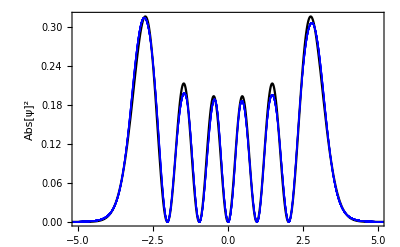

```mathematica
gs = Plot[Evaluate[ψ[5,x]^2],Evaluate@{x,-20,20},PlotRange->All, Frame->True,FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
dataloader = Import["Excited_State_5.txt"];
dataloader = ImportString[dataloader,"Table"]//Flatten;
dataloader = Thread[{xlist,dataloader^2}];
simgs=ListPlot[dataloader,PlotRange->All, Frame->True,PlotStyle->{Blue}, FrameLabel->{"",Text[Style[ToExpression["|\\psi^2|",TeXForm],Medium]]},FrameStyle->Directive[Black,14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Black,Thick[0.01]}];
Show[gs,simgs,PlotRange->{{-5,5},All}]
```